This is based on MWCPlot, originally developed for my presentation in London, but now redisigned (hopefully) to function with sliders as a “Manipulate” object in a CDF.

MWCPlot is quite general; any quantity resulting from the simulation can be plotted against any other resulting quantity. Here I assume that the x-axis will always be PO2, and that users would want to consider how all R, all T, or Y species vary with PO2. 

So here is my list of possible plots:

	0	Y vs. PO2
	1	R0, R1, R2, R3, R4 vs. PO2
	2	All R vs. PO2
	3	1 & 2
	4	1 & 3
	5	T0, T1, T2, T3, T4 vs PO2
	6	All T vs. PO2
	7	1 & 6
	8	1 & 7
	9	1, 2 & 7

```mathematica
MWCGenGraph[
arg_, MWCDataSet_
] := Module[
{
YLIST,
XLIST,
XYLIST,
OUTPUT
},
YLIST = Which[
arg == 0, {#[[3]] & /@ MWCDataSet, Black, "Y"},
arg == 1, {Null, Null},
arg == 2, {#[[5]] / (#[[4]] + #[[5]]) & /@ MWCDataSet, Red, "fR"},
arg == 3, {Null, Null},
arg == 4, {Null, Null},
arg == 5, {Null, Null},
arg == 6, {#[[4]] / (#[[4]] + #[[5]]) & /@ MWCDataSet,Blue, "fT"},
arg == 7, {Null, Null},
arg == 8, {Null, Null},
arg == 9, {Null, Null}
];
XLIST = #[[1]] & /@ MWCDataSet;
XYLIST = Transpose[
{XLIST, YLIST[[1]]}
];
OUTPUT = ListPlot[
XYLIST, 
PlotRange -> {All, {-0.05,1.05}},
PlotStyle -> {YLIST[[2]], PointSize[0.015]},
Axes-> False,
Frame -> True,
FrameLabel -> {"PO2", YLIST[[3]]},
PlotLabel -> YLIST[[3]] <> " vs. " <> "PO2",
ImageSize -> {9 72, 6 72},
TextStyle -> {FontFamily -> "Arial", FontSize-> 18}
]
]
```

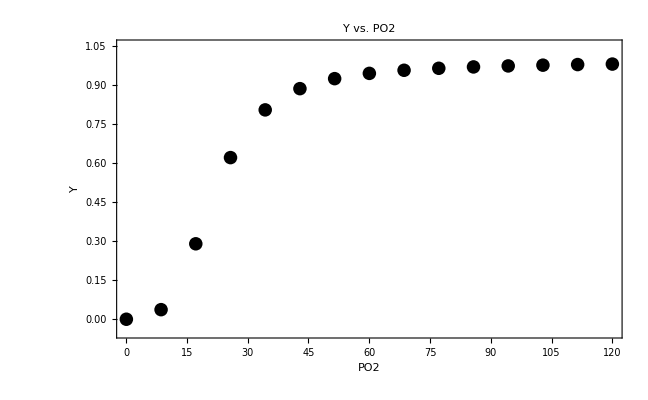

```mathematica
MWCGenGraph[0,mwcsolutionset]
```

```mathematica
Manipulate[
MWCGenGraph[plotnum,mwcsolutionset],
{{plotnum, 0, "Plot Number"}, 0, 9, 1}
]
```